```mathematica
pKxy=-5.5;
pKz=−5.5;
pΓxy=7.6;
pΓz=7.6;
pθ=ArcTan[-2Sqrt[2] pΓxy/(pKxy+pKz-pΓz)]/2+Pi/2;
pϕ=Pi/4;
```

```mathematica
Clear[pKxy,pKz,pΓxy,pΓz,pθ,pϕ]
```

```mathematica
η=Exp[-I qa/2];
A=(pKz Cos[pθ]^2−Sqrt[2]pΓxy  Sin [2 pθ]+(pΓz−pKxy) Sin[pθ] ^2)/2;
B=(η/8)Cos[Sqrt[3] qb/2](3pKxy+pKxy Cos[2pθ]-2Sqrt[2]pΓxy Sin[2pθ]);
CC=(η^2/4)(-pΓz+pKz)Sin[pθ]^2;
CC1=(η^2/4)(pΓz+pΓz Cos[pθ]^2+pKz Sin[pθ]^2)Sin[pθ]^2;
DD=(-η/4)(2Sin[Sqrt[3] qb/2](pKxy Cos[pθ]+Sqrt[2]pΓxy Sin[pθ])+Cos[Sqrt[3]qb/2]Sin[pθ](2Sqrt[2] pΓxy Cos[pθ]+pKxy Sin[pθ]));

DD1=(η/4)(2Sin[Sqrt[3] qb/2](pKxy Cos[pθ]+Sqrt[2]pΓxy Sin[pθ])-Cos[Sqrt[3]qb/2]Sin[pθ](2Sqrt[2] pΓxy Cos[pθ]+pKxy Sin[pθ]));
```

```mathematica
MatrixForm[Table[0,{m,8},{n,8}]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
pH=({{A, Conjugate[CC1], 0, B, 0, Conjugate[CC], 0, DD}, {CC1, A, Conjugate[B], 0, CC, 0, Conjugate[DD], 0}, {0, B, A, Conjugate[CC1], 0, DD1, 0, Conjugate[CC]}, {Conjugate[B], 0, CC1, A, Conjugate[DD1], 0, CC, 0}, {0, Conjugate[CC], 0, DD1, A, Conjugate[CC1], 0, B}, {CC, 0, Conjugate[DD1], 0, CC1, A, Conjugate[B], 0}, {0, DD, 0, Conjugate[CC], 0, B, A, Conjugate[CC1]}, {Conjugate[DD], 0, CC, 0, Conjugate[B], 0, CC1, A}});
```

```mathematica
MatrixForm[Simplify[pH,Assumptions->Element[{pKxy,pKz,pΓxy,pΓz,pθ,pϕ,qa,qb},Reals]]]
```

```mathematica
pHH[qa_,qb_]:=({{1, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, -1, 0, 0, 0}, {0, 0, 0, 0, 0, -1, 0, 0}, {0, 0, 0, 0, 0, 0, -1, 0}, {0, 0, 0, 0, 0, 0, 0, -1}}).({{1/2 (pKz Cos[pθ]^2+(-pKxy+pΓz) Sin[pθ]^2-√2 pΓxy Sin[2 pθ]), 1/4 ⅇ^(ⅈ qa) Sin[pθ]^2 (pΓz+pΓz Cos[pθ]^2+pKz Sin[pθ]^2), 0, 1/8 ⅇ^(-(ⅈ qa)/2) Cos[(√3 qb)/2] (3 pKxy+pKxy Cos[2 pθ]-2 √2 pΓxy Sin[2 pθ]), 0, 1/4 ⅇ^(ⅈ qa) (pKz-pΓz) Sin[pθ]^2, 0, -1/4 ⅇ^(-(ⅈ qa)/2) (Cos[(√3 qb)/2] Sin[pθ] (2 √2 pΓxy Cos[pθ]+pKxy Sin[pθ])+2 (pKxy Cos[pθ]+√2 pΓxy Sin[pθ]) Sin[(√3 qb)/2])}, {1/4 ⅇ^(-ⅈ qa) Sin[pθ]^2 (pΓz+pΓz Cos[pθ]^2+pKz Sin[pθ]^2), 1/2 (pKz Cos[pθ]^2+(-pKxy+pΓz) Sin[pθ]^2-√2 pΓxy Sin[2 pθ]), 1/8 ⅇ^((ⅈ qa)/2) Cos[(√3 qb)/2] (3 pKxy+pKxy Cos[2 pθ]-2 √2 pΓxy Sin[2 pθ]), 0, 1/4 ⅇ^(-ⅈ qa) (pKz-pΓz) Sin[pθ]^2, 0, -1/4 ⅇ^((ⅈ qa)/2) (Cos[(√3 qb)/2] Sin[pθ] (2 √2 pΓxy Cos[pθ]+pKxy Sin[pθ])+2 (pKxy Cos[pθ]+√2 pΓxy Sin[pθ]) Sin[(√3 qb)/2]), 0}, {0, 1/8 ⅇ^(-(ⅈ qa)/2) Cos[(√3 qb)/2] (3 pKxy+pKxy Cos[2 pθ]-2 √2 pΓxy Sin[2 pθ]), 1/2 (pKz Cos[pθ]^2+(-pKxy+pΓz) Sin[pθ]^2-√2 pΓxy Sin[2 pθ]), 1/4 ⅇ^(ⅈ qa) Sin[pθ]^2 (pΓz+pΓz Cos[pθ]^2+pKz Sin[pθ]^2), 0, 1/4 ⅇ^(-(ⅈ qa)/2) (-Cos[(√3 qb)/2] Sin[pθ] (2 √2 pΓxy Cos[pθ]+pKxy Sin[pθ])+2 (pKxy Cos[pθ]+√2 pΓxy Sin[pθ]) Sin[(√3 qb)/2]), 0, 1/4 ⅇ^(ⅈ qa) (pKz-pΓz) Sin[pθ]^2}, {1/8 ⅇ^((ⅈ qa)/2) Cos[(√3 qb)/2] (3 pKxy+pKxy Cos[2 pθ]-2 √2 pΓxy Sin[2 pθ]), 0, 1/4 ⅇ^(-ⅈ qa) Sin[pθ]^2 (pΓz+pΓz Cos[pθ]^2+pKz Sin[pθ]^2), 1/2 (pKz Cos[pθ]^2+(-pKxy+pΓz) Sin[pθ]^2-√2 pΓxy Sin[2 pθ]), 1/4 ⅇ^((ⅈ qa)/2) (-Cos[(√3 qb)/2] Sin[pθ] (2 √2 pΓxy Cos[pθ]+pKxy Sin[pθ])+2 (pKxy Cos[pθ]+√2 pΓxy Sin[pθ]) Sin[(√3 qb)/2]), 0, 1/4 ⅇ^(-ⅈ qa) (pKz-pΓz) Sin[pθ]^2, 0}, {0, 1/4 ⅇ^(ⅈ qa) (pKz-pΓz) Sin[pθ]^2, 0, 1/4 ⅇ^(-(ⅈ qa)/2) (-Cos[(√3 qb)/2] Sin[pθ] (2 √2 pΓxy Cos[pθ]+pKxy Sin[pθ])+2 (pKxy Cos[pθ]+√2 pΓxy Sin[pθ]) Sin[(√3 qb)/2]), 1/2 (pKz Cos[pθ]^2+(-pKxy+pΓz) Sin[pθ]^2-√2 pΓxy Sin[2 pθ]), 1/4 ⅇ^(ⅈ qa) Sin[pθ]^2 (pΓz+pΓz Cos[pθ]^2+pKz Sin[pθ]^2), 0, 1/8 ⅇ^(-(ⅈ qa)/2) Cos[(√3 qb)/2] (3 pKxy+pKxy Cos[2 pθ]-2 √2 pΓxy Sin[2 pθ])}, {1/4 ⅇ^(-ⅈ qa) (pKz-pΓz) Sin[pθ]^2, 0, 1/4 ⅇ^((ⅈ qa)/2) (-Cos[(√3 qb)/2] Sin[pθ] (2 √2 pΓxy Cos[pθ]+pKxy Sin[pθ])+2 (pKxy Cos[pθ]+√2 pΓxy Sin[pθ]) Sin[(√3 qb)/2]), 0, 1/4 ⅇ^(-ⅈ qa) Sin[pθ]^2 (pΓz+pΓz Cos[pθ]^2+pKz Sin[pθ]^2), 1/2 (pKz Cos[pθ]^2+(-pKxy+pΓz) Sin[pθ]^2-√2 pΓxy Sin[2 pθ]), 1/8 ⅇ^((ⅈ qa)/2) Cos[(√3 qb)/2] (3 pKxy+pKxy Cos[2 pθ]-2 √2 pΓxy Sin[2 pθ]), 0}, {0, -1/4 ⅇ^(-(ⅈ qa)/2) (Cos[(√3 qb)/2] Sin[pθ] (2 √2 pΓxy Cos[pθ]+pKxy Sin[pθ])+2 (pKxy Cos[pθ]+√2 pΓxy Sin[pθ]) Sin[(√3 qb)/2]), 0, 1/4 ⅇ^(ⅈ qa) (pKz-pΓz) Sin[pθ]^2, 0, 1/8 ⅇ^(-(ⅈ qa)/2) Cos[(√3 qb)/2] (3 pKxy+pKxy Cos[2 pθ]-2 √2 pΓxy Sin[2 pθ]), 1/2 (pKz Cos[pθ]^2+(-pKxy+pΓz) Sin[pθ]^2-√2 pΓxy Sin[2 pθ]), 1/4 ⅇ^(ⅈ qa) Sin[pθ]^2 (pΓz+pΓz Cos[pθ]^2+pKz Sin[pθ]^2)}, {-1/4 ⅇ^((ⅈ qa)/2) (Cos[(√3 qb)/2] Sin[pθ] (2 √2 pΓxy Cos[pθ]+pKxy Sin[pθ])+2 (pKxy Cos[pθ]+√2 pΓxy Sin[pθ]) Sin[(√3 qb)/2]), 0, 1/4 ⅇ^(-ⅈ qa) (pKz-pΓz) Sin[pθ]^2, 0, 1/8 ⅇ^((ⅈ qa)/2) Cos[(√3 qb)/2] (3 pKxy+pKxy Cos[2 pθ]-2 √2 pΓxy Sin[2 pθ]), 0, 1/4 ⅇ^(-ⅈ qa) Sin[pθ]^2 (pΓz+pΓz Cos[pθ]^2+pKz Sin[pθ]^2), 1/2 (pKz Cos[pθ]^2+(-pKxy+pΓz) Sin[pθ]^2-√2 pΓxy Sin[2 pθ])}})
```

```mathematica
MatrixForm[KroneckerProduct[PauliMatrix[3],IdentityMatrix[4]]]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

```mathematica
pEE[qa_,qb_]:=Sort[Re[Eigenvalues[pHH[qa/3,qb/Sqrt[3]]]]]
```

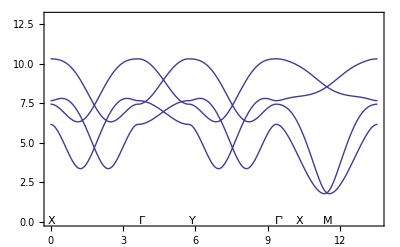

```mathematica
Plot[Piecewise[{{pEE[0,(t-2Pi/Sqrt[3])Sqrt[3]],t≥0&&t<2Pi/Sqrt[3]},{pEE[(t-2Pi/Sqrt[3])*3,0],t≥2Pi/Sqrt[3]&&t<(2Pi/Sqrt[3]+2Pi/3)},{pEE[2Pi,Sqrt[3](t-(2Pi/Sqrt[3]+2Pi/3))],t≥(2Pi/Sqrt[3]+2Pi/3)&&t<(4Pi/Sqrt[3]+2Pi/3)},{pEE[3*((4Pi/Sqrt[3]+2Pi/3)-t)/2+2Pi,2Pi+3*((4Pi/Sqrt[3]+2Pi/3)-t)/2],t≥(4Pi/Sqrt[3]+2Pi/3)&&t<(4Pi/3+4Pi/Sqrt[3])},{pEE[Pi+3*((4Pi/3+4Pi/Sqrt[3])-t)/2,Pi+3*((4Pi/3+4Pi/Sqrt[3])-t)/2],t≥(4Pi/3+4Pi/Sqrt[3])&&t<(2Pi+4Pi/Sqrt[3])}}],{t,0,2Pi+4Pi/Sqrt[3]},GridLines->{{{2Pi/Sqrt[3],Dashed},{2Pi/Sqrt[3]+2Pi/3,Dashed},{4Pi/Sqrt[3]+2Pi/3,Dashed},{4Pi/3+4Pi/Sqrt[3],Dashed}},{}},Epilog->{Inset["X",{0.05,0.08}],Inset["Γ",{2Pi/Sqrt[3]+0.15,0.08}],Inset["Y",{2Pi/Sqrt[3]+2Pi/3+0.15,0.08}],Inset["Γ'",{4Pi/Sqrt[3]+2Pi/3+0.15,0.08}],Inset["M",{4Pi/3+4Pi/Sqrt[3]+0.05,0.08}],Inset["X",{4Pi/3+2Pi-0.15,0.08}]},Frame->True,PlotRange->{{0,2Pi+4Pi/Sqrt[3]},{0,13}}]
```